```mathematica
Plot3D[x^2+y^2,{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
{3, 4}.{3,4}
{5,6}.{5,6}
```

25

61

```mathematica
f[x_]:=x.x
f[{x,y}]
Simplify[f'[{x,y}]]
Grad[f[{x,y}],{x,y}]//MatrixForm
Plot3D[f[{x,y}],{x,-1,1},{y,-1,1}]
```

x^2+y^2

1.{x,y}+{x,y}.1

(2 x
2 y)

-Graphics3D-

```mathematica
f2[x_,y_]:=x^2+y^2
Grad[f2[x,y],{x,y}]
```

{2 x,2 y}

```mathematica
fHole[x_]:=1-Exp[-x.x]
fHole'[x]
fHole'[{x,y}]
Grad[fHole[{x,y}],{x,y}]
Plot3D[fHole[{x,y}],{x,-1,1},{y,-1,1}]
```

-ⅇ^(-x.x) (-1.x-x.1)

-ⅇ^(-x^2-y^2) (-1.{x,y}-{x,y}.1)

{2 ⅇ^(-x^2-y^2) x,2 ⅇ^(-x^2-y^2) y}

-Graphics3D-

```mathematica
f3[x_]:=1-Exp[-x.x]

f3[{x,y}]
f3[{c1 x,c2 y}]
-f3[{c1 x,c2 y}]+1
Grad[f3[{x,y}],{x,y}]
Grad[f3[{c1 x,c2 y}],{x,y}]
```

1-ⅇ^(-x^2-y^2)

1-ⅇ^(-c1^2 x^2-c2^2 y^2)

ⅇ^(-c1^2 x^2-c2^2 y^2)

{2 ⅇ^(-x^2-y^2) x,2 ⅇ^(-x^2-y^2) y}

{2 c1^2 ⅇ^(-c1^2 x^2-c2^2 y^2) x,2 c2^2 ⅇ^(-c1^2 x^2-c2^2 y^2) y}

```mathematica
Solve[x^2+y^2==1&&2== 2*lam*x&&1== 2*lam*y,{x,y,lam}]
```

{{x→-2/(√5),y→-1/(√5),lam→-(√5)/2},{x→2/(√5),y→1/(√5),lam→(√5)/2}}

## Day 2 - Interior Point Log Barrier

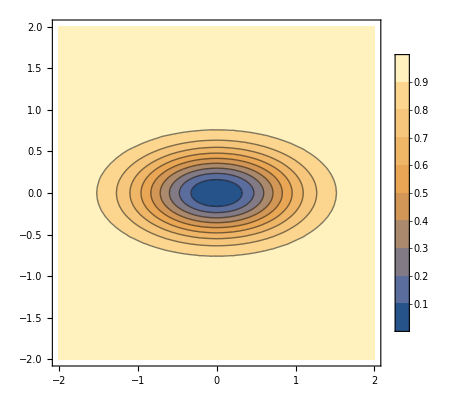

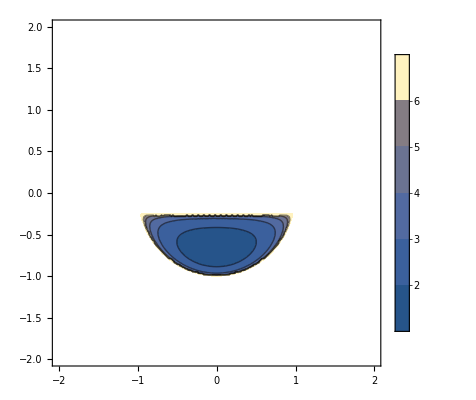

```mathematica
g1[x_, y_]:=x^2+y^2-1
g2[x_,y_]:=y +1/4

fFun[x_,y_]:=1-Exp[-(x^2+4 y^2)]

ContourPlot[fFun[x,y],{x,-2,2},{y,-2,2},PlotLegends->Automatic,PlotRange->All]

ContourPlot[(-Log[-g1[x,y]]-Log[-g2[x,y]]),{x,-2,2},{y,-2,2},PlotLegends->Automatic,PlotRange->Full]
```

```mathematica
Manipulate[ContourPlot[fFun[x,y]+mu*(-Log[-g1[x,y]]-Log[-g2[x,y]]),{x,-2,2},{y,-2,2},PlotRange->Full,PlotLegends->Automatic],{mu,0.00001,1}]
```

```mathematica
Minimize[fFun[x,y],{x,y}][[2]][[1]][[2]]
```

0

```mathematica
Minimize[fFun[x,y],{x,y}]
centralPath=Table[{NMinimize[{fFun[x,y]+Re[1/mu*(-Log[-g1[x,y]]-Log[-g2[x,y]])],g1[x,y]<0&&g2[x,y]<0},{x,y}][[2]][[1]][[2]],NMinimize[{fFun[x,y]+Re[1/mu*(-Log[-g1[x,y]]-Log[-g2[x,y]])],g1[x,y]<0&&g2[x,y]<0},{x,y}][[2]][[2]][[2]]},{mu,0.1,100}];
```

{0,{x→0,y→0}}

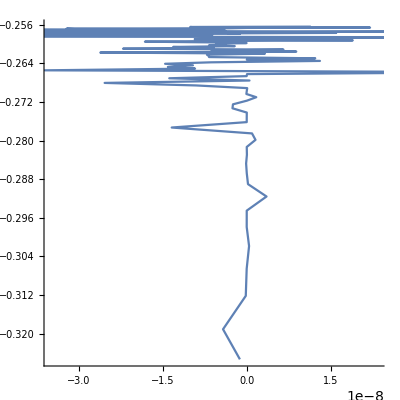

```mathematica
ListLinePlot[centralPath,AspectRatio->1]
```